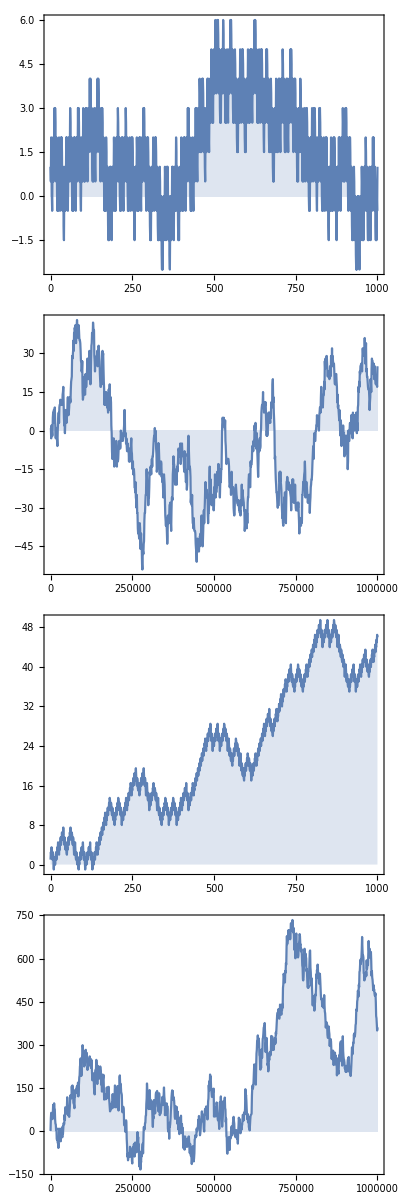

```mathematica
Column[ListLinePlot[#1,]&@@@
(*({ResourceFunction["CyclicTagSystemEvolveList"][#[[1]],{1},#[[2]],#[[2]]/1000,"Lengths"]-(Total[Flatten[#[[1]]]]/Length[#[[1]]]-1) Range[0,#[[2]],#[[2]]/1000],#[[2]]}&/@Flatten[Table[{rule,range},{rule,{{{1},{1,0,1}},{{1,1,1},{0}}}},{range,{10^3,10^6}}],1])*)]
```